# Lab 5: Integration -- Carter Colton

```mathematica
Clear["`*" ]
```

## Assignment 1: Two Basic Integrals

(a) Integrate J_1(x) as an indefinite integral. Plot the integral and integrand together, over the range {x, 0, 20}.  As mentioned in the Differentiation lab, this is a Bessel function (of the “first kind”), used by physicists in problems involving waves with circular boundaries. It’s obtained in Mathematica via BesselJ. The integral of J_1 is related to J_0. 
(b) Compute ∫_(-∞)^∞ e^(-x^2)dx, a definite integral.  This represents the total area under the e^(-x^2) function, so I’d like you to also plot that function using the Filling → Axis option to visualize it. Have your plot go from -5 to 5.

```mathematica
j1=Integrate[BesselJ[0,x],x]
```

x HypergeometricPFQ[{1/2},{1,3/2},-x^2/4]

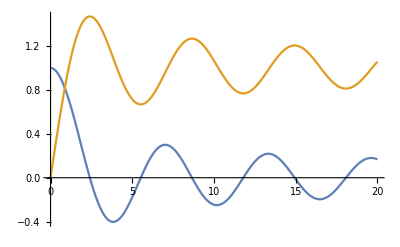

```mathematica
Plot[{BesselJ[0,x], j1}, {x,0,20}]
```

```mathematica
Integrate[E^(-x^2),{x,-Infinity,Infinity}]
```

√π

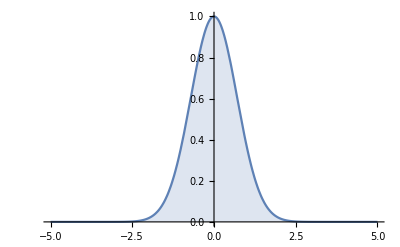

```mathematica
Plot[E^(-x^2),{x,-5,5},Filling->Axis]
```

## Assignment 2: How Long is a Parabola

(a) Consider the section of parabola defined by the equation y = 1-x^2 over the range -1 < x < 1. Make a plot of y(x), and give a rough estimate (but as accurate as you can) of the total length of that curve.
(b) Find the derivative, dy/dx, and use it in the path length formula to determine the precise value of the path length (in decimal format).

```mathematica
f[x_]=1-x^2
```

1-x^2

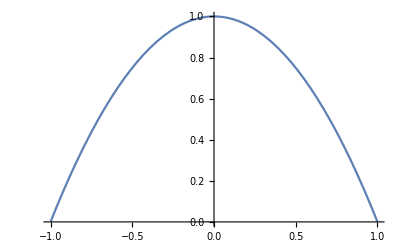

```mathematica
Plot[f[x],{x,-1,1}]
```

My estimate for this arc length is: 2sqrt(2)

```mathematica
df=D[f[x],x]
```

-2 x

```mathematica
N[Integrate[Sqrt[1+df^2],{x,-1,1}]]
```

2.95789

Compare that to my estimate

```mathematica
N[2Sqrt[2]]
```

2.82843

It is pretty close

## Assignment 3: Sines and Cosines

```mathematica
Clear["`*" ]
```

Note: Using Assumptions inside an Integrate command is apparently not quite identical to using the Assuming command. When using the former, I sometimes have to additionally use the Refine command to get it fully simplified, as in “Refine[%, {n∈Integers, m ∈Integers}]”. Unfortunately I haven’t yet been able to figure out a pattern for when that will/will not be neccesary. It was necessary a couple of times for me when I did the following assignment.

(a1) Show that all sin(nx) and sin(mx) functions are orthogonal to each other over the integral 0 to 2π, when n does not equal m. Use Assuming or Assumptions to specify that n ≠ m, and that both n and m are integers. 
(a2) Find the value of the integral of sin(nx) sin(mx) when n and m are equal. (Again, use an assumption to specify that n==m. Note the double equals sign there.) 
(b) Repeat part (a), for cos(nx) and cos(mx).
(c) Repeat, for sin(nx) and cos(mx).

Summary: You should have found that sine and cosine functions are always orthogonal, that sine functions are orthogonal to each other when n and m are not equal, and that cosine functions are similarly orthogonal when n ≠ m.

Final words: Orthogonal functions are incredibly important in physics applications and will be a major part of your study in Phys 318, 441, and 452, just to name a few courses. Sines/cosines are just one set of orthogonal functions. Two other important sets include the Bessel functions and the Legendre polynomials (see below for an extra credit problem involving the Legendre polynomials).

```mathematica
f1=Sin[n*x]
f2=Sin[m*x]
f3=Cos[n*x]
f4=Cos[m*x]
```

Sin[n x]

Sin[m x]

Cos[n x]

Cos[m x]

```mathematica
Assuming[{n≠ m,n∈Integers,m∈Integers},Integrate[f1*f2, {x,0,2*Pi}]]
```

0

```mathematica
Assuming[{n== m,n∈Integers,m∈Integers},Integrate[f1*f2, {x,0,2*Pi}]]
```

π

```mathematica
Assuming[{n≠ m,n∈Integers,m∈Integers},Integrate[f3*f4, {x,0,2*Pi}]]
```

0

```mathematica
Assuming[{n== m,n∈Integers,m∈Integers},Integrate[f3*f4, {x,0,2*Pi}]]
```

π

```mathematica
Assuming[{n≠ m,n∈Integers,m∈Integers},Integrate[f1*f4, {x,0,2*Pi}]]
```

0

```mathematica
Assuming[{n== m,n∈Integers,m∈Integers},Integrate[f1*f4, {x,0,2*Pi}]]
```

0

## Assignment 4: Performing 3 Multi-Variable Integrals

Compute the following integrals.
(a) Compute the indefinite integral ∫∫sin(x y)dx dy.  Plot3D the integrand and the integral on the same graph over the range {x, -π, π} and  {y, -π, π}.  Use the PlotStyle option to give the two surfaces different colors.  (The CosIntegral function that should appear in your result is another of Mathematica’s many built-in functions. You can see what shape it takes by viewing the help file.)
(b) Compute the definite integral ∫∫(x^2+y^2)dx dy, with x and y both ranging from -2 to 2. Plot3D the integrand over the same range and use the PlotRange->All and Filling->Axis options to visualize the region of space whose volume you have just calculated.
(c) In spherical coordinates, dx dy dz translates to r^2 sinθ dϕ dθ dr.  Here r is the distance from the origin to an arbitrary point (x,y,z).  θ is the angle the (x,y,z) vector makes with respect to the z-axis, and ϕ is the angle the projection of the (x,y,z) vector onto the x-y plane makes with respect to the x-axis. (Careful: this is the usual definition for physics classes but math classes often define θ and ϕ the opposite way.) Thus to cover all points inside a sphere of radius R: r ranges from 0 to R, θ ranges from 0 to π, and ϕ ranges from 0 to 2π. Let the function you are integrating be equal to 1 everywhere, and compute the integral ∫∫∫dx dy dz expressed in spherical coordinates to obtain the well-known expression for the volume of a sphere.

```mathematica
Integrate[Sin[x*y], x,y]
```

-CosIntegral[x y]

```mathematica
fintegral=%
```

-CosIntegral[x y]

```mathematica
Plot3D[{Sin[x*y],fintegral},{x,-Pi,Pi},{y,-Pi,Pi}]
```

-Graphics3D-

```mathematica
Integrate[x^2+y^2,{x,-2,2},{y,-2,2}]
```

128/3

```mathematica
Plot3D[x^2+y^2,{x,-2,2},{y,-2,2},PlotRange->All, Filling->Axis]
```

-Graphics3D-

```mathematica
Integrate[(r^2)*Sin[theta],{r,0,R},{theta,0,Pi},{phi,0,2*Pi}]
```

(4 π R^3)/3

## Assignment 5: The Area of a Circle 2 Ways

(a) Determine the area of a circle (radius 1) by using a conventional 1D integral in x. (Hint: use the equation of a circle, x^2+ y^2=1 to solve for y.) Think carefully about your limits of integration and what the integral represents. A Plot command with Filling->Axis may help.
(b) Determine the area of the same circle by using RegionPlot (and Plot3D if you wish) to visualize the inquality x^2+y^2≤ 1, then Boole and Integrate to determine the area inside the circle.

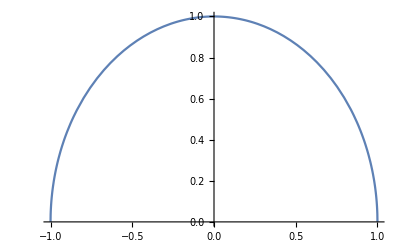

```mathematica
Plot[Sqrt[1-x^2], {x,-1,1}]
```

This only gives half of the circle, so we need to multiply our integral by 2.

```mathematica
Integrate[2*Sqrt[1-x^2],{x,-1,1}]
```

π

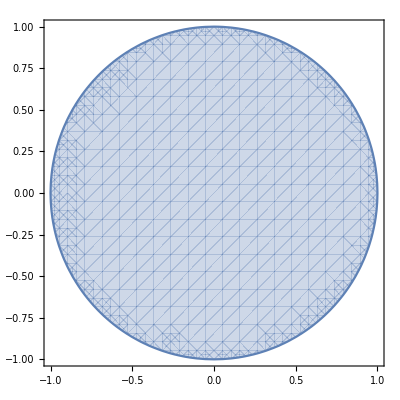

```mathematica
RegionPlot[x^2+y^2≤1, {x,-1,1},{y,-1,1}]
```

```mathematica
Integrate[Boole[x^2+y^2≤1],{x,-1,1},{y,-1,1}]
```

π

## Assignment: Dealing with a Singularity

(a) Make a plot of e^(-(x-1)^2), from -1000 to 1000. It’s not really a singularity (as you can see by making the plot range much smaller), but on that large of a scale it acts like one.

(b) If you try to NIntegrate this function over the range fom -1000 to 1000, it will give you an error message and a wrong result.

```mathematica
NIntegrate[Exp[-(x-1)^2],{x,-1000,1000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.87517}. NIntegrate obtained 1.63305 and 0.00473656 for the integral and error estimates.

1.63305

(I know the result is wrong, because I happen to know the answer should be extremely close to sqrt(π). That’s because when the limits are from -∞ to ∞, it’s essentially the integral you did for assignment 1b.)

The main way to automatically deal with singularities in integrals is to specify a point or points that Mathematica should pay special attention to as it’s going through its numerical algorithm. The Numerical Integration tutorial linked to above shows how to do that. After consulting the tutorial, redo the numerical integral, this time specifying x=1 as one such special point.

(c) Unfortunately, even after you specify the point x=1 as a possible singularity, for this particular problem Mathematica still gives you the wrong answer. And it probably won’t even give you any error messages as a warning this time. Remember, Mathematica is not infallible! For critical calculations you should always think about, and possibly double-check, the answers it gives you. That being said, Mathematica is still the top-of-the-line computational mathematical program. It’s not perfect, but it’s very, very good at what it does. 

To make an even better calculation, try using the MaxPoints, MinRecursion, and/or MaxRecursion options. One of them, or possibly a combination, will give you the correct result.

```mathematica
function=E^-(x-1)^2
```

ⅇ^(-(-1+x)^2)

General::munfl: Exp[-1.00192×10^6] is too small to represent as a normalized machine number; precision may be lost.

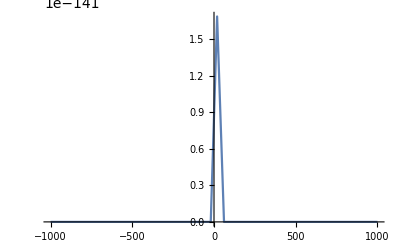

```mathematica
Plot[function,{x,-1000,1000}]
```

This is what my answer should look like

```mathematica
N[Sqrt[Pi]]
```

1.77245

```mathematica
NIntegrate[Exp[-(x-1)^2],{x,-1000,1,1000}]
```

0.886227

```mathematica
NIntegrate[Exp[-(x-1)^2],{x,-1000,1,1000},MinRecursion->3,MaxRecursion->20]
```

1.77245

## Assignment 7: Solving a Problem with an Advanced Method

Find the section on Duffy Coordinates in the integration strategies tutorial, and figure out how to use that method (specifying the problematic corner) to get an answer to the 1/Sqrt[x^2+y^2] integral in about a second or less, still using a WorkingPrecision of 30.

```mathematica
NIntegrate[1/(√(x^2+y^2)),{x,0,1},{y,0,1},Method->{"DuffyCoordinates","Corners"->{0,0}},WorkingPrecision->30]
```

1.76274717403908605046521865045

## Assignment 8: Electric Potential From a Spherical Shell Charge Distribution

(a) Perform the integral to get the potential as a function of r.  Hint: Remember to let Mathematica know that r > 0 and R > 0. If you find the integral taking more than a few seconds, or if it gives you bizarre output, try reversing the order you tell Mathematica to perform the θ and ϕ integrals. While that shouldn’t matter--and didn’t to me--it seemed to, to some students in a previous semester.
(b) Now use variable replacement to evaluate your potential for the simple case where {k → 1, Q → 1, R → 1}.  The resulting expression should depend only on r. Plot it over the range 0 < r < 5, using PlotRange→{0, 1.1} as an option.  Interpret this (perhaps surprising) result to your TA. Incidentally, since gravity is also an inverse square law and since field is essentially the derivative of the potential, your result should prove that if the earth were a hollow sphere, there would be no gravitational field on the inside.

Thus the total potential at (x,y,z) is V(r) = ∫(k dQ)/distance=∫(k  Q/(4 πR^2)  dA)/(√(R^2+r^2-2R r cosθ)). In spherical coordinates,  dA = R^2 sinθ dθ dϕ, and the integral goes from 0 to 2π in ϕ and from 0 to π in θ

```mathematica
Clear[k,Q,R]
```

```mathematica
integrand =(k Q)/(4 π R^2)(R^2 Sin[theta])/Sqrt[R^2 + r^2 - 2 R r Cos[theta]]
potential=Integrate[integrand,{phi,0,2*Pi},{theta,0,Pi}, Assumptions->{R>0,r>0, r ≠ R}]
```

(k Q Sin[theta])/(4 π √(r^2+R^2-2 r R Cos[theta]))

(k Q (r+R-Abs[r-R]))/(2 r R)

```mathematica
newpotential = potential/.{k->1,Q->1,R->1}
```

(1+r-Abs[-1+r])/(2 r)

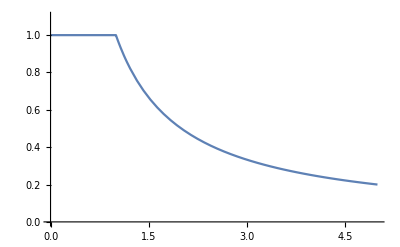

```mathematica
Plot[newpotential,{r,0,5}, PlotRange->{0,1.1}]
```

## Assignment 9: Monte Carlo Integration of a Circle

The purpose of this assignment is to create your own Mathematica function which performs a Monte Carlo integral, without using NIntegrate.

(a) Create the function circ[x_] := Sqrt[1-x^2] and plot it over the range {x, -1, 1} with AspectRatio → Automatic and Filling → Axis.  NIntegrate the function over the same range. It’s half of a circle with radius 1, so the area should obviously be π/2.
(b) Now, create a function called montecirc[n_]. The purpose of this function is to implement the Monte Carlo method using the summation formula in the description above (i.e. not by using NIntegrate). The function argument n indicates the number of random points to use in the summation. Specifically, your function should create a list of n random numbers inside the domain, evaluate circ(x) at those points, sum the function evaluations together with Total, and finally multiply everything by (b-a)/n. Calculate montecirc[n] for n = 10^1, 10^2, 10^3, 10^4, 10^5 and 10^6. For each result calculate the fractional error between your result and the true value of the integral: (result - true)/true. Your fractional error should decrease as you use more and more random points in your function.

```mathematica
circ[x_]:=Sqrt[1-x^2]
```

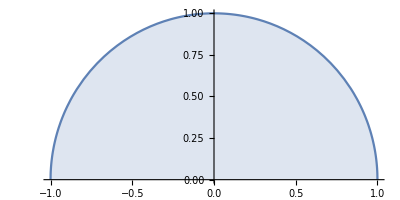

```mathematica
Plot[circ[x], {x,-1,1}, AspectRatio->Automatic, Filling->Axis]
```

```mathematica
true = NIntegrate[circ[x],{x,-1,1}]
```

1.5708

```mathematica
N[Pi/2]
```

1.5708

```mathematica
Clear[n]
montecirc[n_] := 2/n Total[circ[RandomReal[{-1, 1}, n]]]
evaluated = Table[montecirc[10^n],{n, 1, 6}]
(evaluated-true)/true
```

{1.60751,1.49461,1.58144,1.57052,1.5726,1.57051}

{0.0233712,-0.0485002,0.00677709,-0.000178798,0.00114799,-0.0001829}